```mathematica
Get["RootSearch`"]
```

```mathematica
?RootSearch
```

RootSearch[lhs==rhs,{x,xmin,xmax}] tries to find all numerical solutions to the equation (lhs==rhs) with values of x between xmin and xmax.

```mathematica
(*Data*)
nperiods =1000;
μ=3.9877848 10^14;
Mp=1000;
l=50000;
a=6870000;
τ =- 2*10^7;


period = 2 π √(a^3/μ);
ranget = nperiods*period;

psiQ =τ ;


(*Position vectorc and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc[t] Cos[θ[t]]}, {rc[t] Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});
rp2[t]=rm[t]-({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp) (rc'[t]^2+rc[t]^2 θ'[t]^2);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{0}, {0}, {(θ'[t]+ψ'[t])}});

Subscript[ⅈ, 123]=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}});

Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Subscript[U, p1]=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Subscript[U, p2]=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
V=Subscript[U, p1]+Subscript[U, p2];

L=T-V;
eqn1=Simplify[D[D[L, ψ'[t]], t]-D[L, ψ[t]]-psiQ];
eqn2 = Simplify[D[D[L, θ'[t]], t]-D[L, θ[t]]];
eqn3 = Simplify[D[D[L, rc'[t]], t]-D[L, rc[t]]];
```

```mathematica
systemfunc[e_]:=(

psi0 = 0;
psidsh0 =0;

r0 = a (1-e);
rdsh0 = 0;

theta0 = 0;
thetadsh0=1/r0*√((μ (1+e))/(a (1-e)))  ;

system=NDSolve[{eqn1==0,eqn2==0,eqn3==0,
ψ[0]==psi0,ψ'[0]==psidsh0, θ[0] == theta0,θ'[0]==thetadsh0,rc[0] == r0,rc'[0]==0},
{ψ,θ,rc},{t,0,ranget},
MaxSteps->∞,AccuracyGoal->Automatic];
psis[t_]:=ψ[t]/.system[[1]];
psidhs[t_]:=ψ'[t]/.system[[1]];
rvs[t_] :=rc'[t]/.system[[1]];
as[t_]:=rc''[t]/.system[[1]];
rs[t_]:=rc[t]/.system[[1]];
thetas[t_]:=θ[t]/.system[[1]]

)
```

```mathematica
rootsearchrange = 20;

seques = {};
rvalss = {};
ess = {};
ass={};
Do[Print[eee];
systemfunc[eee];
rootst = {};
Do[rootst = Append[rootst,RootSearch[rvs[t]==0,{t,period*n,(n+rootsearchrange)*period}]],{n,0,nperiods-rootsearchrange,rootsearchrange}];
rootst = Flatten[rootst];
roots = {};
Do[roots = Append[roots,t/.rootst[[n]]],{n,1,Length[rootst]}];
rvals = {};
sequed = {};
es={};
ars={};
Do[rvals=Append[rvals,{roots[[n]],rs[roots[[n]]]}],{n,1,Length[roots]}];
rvalss=Append[rvalss,rvals];
Do[If[Not[0.995  rvals[[n-1]][[2]]<rvals[[n]][[2]]<1.005 rvals[[n-1]][[2]]],sequed=Append[sequed,rvals[[n]]]],{n,2,Length[rvals]}];
If[sequed[[1]][[2]]<sequed[[2]][[2]],sequed = Drop[sequed,1]];

Do[ra = sequed[[n]][[2]];rp = sequed[[n+1]][[2]];es = Append[es,{sequed[[n]][[1]],(ra-rp)/(ra+rp)}];ars=Append[ars,{sequed[[n]][[1]],(ra+rp)/2}],{n,1,Length[sequed]-1,2}];
ess = Append[ess,es];
seques = Append[seques,sequed];
ass = Append[ass,ars],
{eee,0.7,0.7,0.1}]
```

0.7

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision::precset will be suppressed during this calculation.

```mathematica
Manipulate[ListPlot[ass[[n]]],{n,1,Length[ess],1}]
```

```mathematica
ra
```

1.26292×10^7

```mathematica
rp
```

2.25807×10^6

```mathematica
(ra-rp)/(ra+rp)
```

0.696644

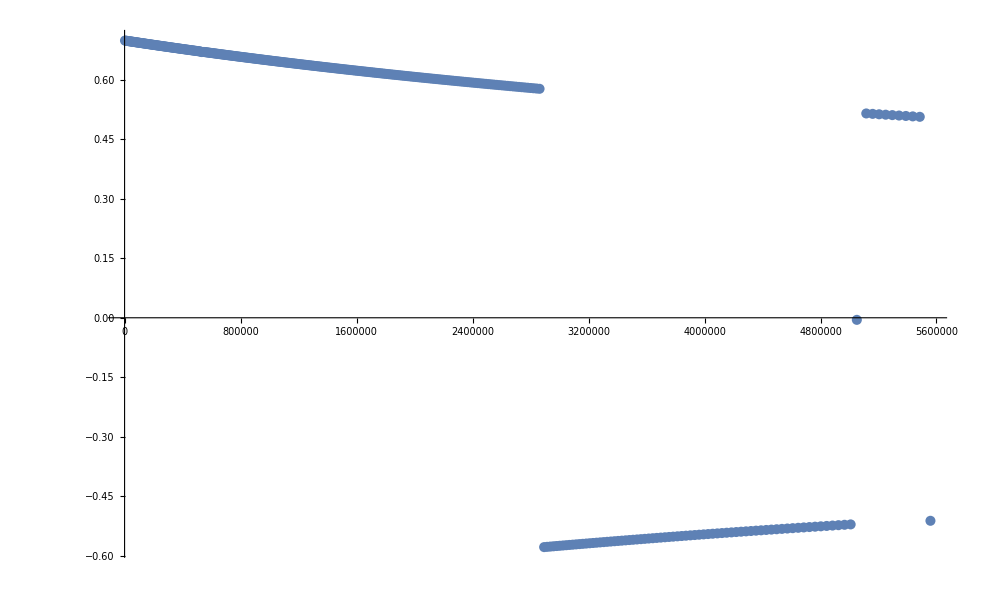

```mathematica
ListPlot[ess[[1;;-1]]]
```